## Simple 2D Linear Triangular Finite Element

## Defined Function

```mathematica
(* locator local to global *)
tr[ne_]:=Table[Sequence@@{elnode[[ne,i]]*2-1,elnode[[ne,i]]*2},{i,Length[elnode[[ne]]]}] (* tr/mapping node coordinate to dof as given element number *)
```

```mathematica
(* module matrix reducer *)
reducer[
m_?MatrixQ,rows:{___Integer},cols:{___Integer}]:=
Part[
Delete[m,List/@rows],All,Complement[Range@Length@m[[1]],cols]]
```

```mathematica
elcoor[ne_] := ncoor[[elnode[[ne]]]]; (* coordinate of node that construct element *)
```

```mathematica
(* element area *)
A[elementnumber_]:=
Module[{en=elementnumber,temp,x1,y1,x2,y2,x3,y3},
x1=Part[elcoor[en],1,1];y1=Part[elcoor[en],1,2];x2=Part[elcoor[en],2,1];y2=Part[elcoor[en],2,2];x3=Part[elcoor[en],3,1];y3=Part[elcoor[en],3,2];
temp=(x1(y2-y3)+x2(y3-y1)+x3(y1-y2))/2;Return[temp]
]
```

```mathematica
(* gradient matrix *)
BM[elementnumber_]:=
Module[{en=elementnumber,temp,x1,y1,x2,y2,x3,y3,Q1,Q2,Q3,R1,R2,R3},
x1=Part[elcoor[en],1,1];y1=Part[elcoor[en],1,2];x2=Part[elcoor[en],2,1];y2=Part[elcoor[en],2,2];x3=Part[elcoor[en],3,1];y3=Part[elcoor[en],3,2];
Q1=y2-y3;Q2=y3-y1;Q3=y1-y2;R1=x3-x2;R2=x1-x3;R3=x2-x1;
temp=(0.5A[en]){
{Q1,0,Q2,0,Q3,0},
{0,R1,0,R2,0,R3},
{R1,Q1,R2,Q2,R3,Q3}
}; Return[temp]
]
```

```mathematica
CM = Emod/(1-v^2){{1,v,0},{v,1,0},{0,0,(1-v)/2}};(* stress-strain matrix *)
```

```mathematica
km[en_] := thk  A[en]*Transpose@BM[en].CM.BM[en];(* local stiffness *)
```

```mathematica
(* averaging variables that located in 3 or 4 Gauss points*)
nodalAverage[variable_]:=
Module[{s=variable,temp },
temp=Array[0 &,{Length[node],1}];
Do[
Part[temp,element[[ne]]]+= s[[ne]]
,{ne, Length[element]}];
Do[
temp[[n]]=temp[[n]]/Count[Flatten@element,n]
,{n, Length[node]}];temp=Flatten@temp;Return[temp]
]
```

```mathematica
plottingResult[var_,unit_,title_]:=
Module[{v=var,u=unit,t=title,minvar,maxvar,minnode,maxnode,mincoor,maxcoor,varcoor,minl,maxl},
varcoor=MapThread[Join[#1,{#2}]&,{dcoor,v}];
maxvar=Max[v];minvar=Min[v];
maxnode=Flatten@Position[v,maxvar];minnode=Flatten@Position[v,minvar];maxcoor=Flatten@dcoor[[maxnode]];mincoor=Flatten@dcoor[[minnode[[1]]]];
minl="min "<>ToString@InputForm[minvar,NumberMarks->False];
maxl="max "<>ToString@InputForm[maxvar,NumberMarks->False];
plotb=ListContourPlot[varcoor,ColorFunction->"Rainbow",AspectRatio->Automatic,PlotRange->All,Contours->12,ContourStyle->None,PlotLabel->ToString[t],Frame-> False,PlotRangePadding->0.6, ImagePadding -> {{1,1}, {1,1}},PlotLegends->{
Placed[BarLegend[Automatic,LegendLabel->ToString[u]],Right],
Placed[PointLegend[{Blue,Red},{minl ,maxl }, LabelStyle->12,LegendLayout-> "Column",LegendFunction -> "Frame",LegendMargins->{{20, 20}, {5, 5}}],Below]
}];;
plotorigin=MeshRegion[ncoor,Polygon/@elnode,MeshCellStyle->{0-> {PointSize[Small],Black},1-> {White,Opacity[0.2]},2->Opacity[0]}];
plotdeform=MeshRegion[dcoor,Polygon/@elnode,MeshCellStyle->{0-> {PointSize[Small],Black},1-> {Red,Opacity[0.2]},2->Opacity[0]}];
plotnode=HighlightMesh[plotorigin,Labeled[0,"Index",{Top,Right}]];
plotc=Graphics[{PointSize[0.03],Point[{mincoor,maxcoor},VertexColors->{Blue,Red}]}];Show[plotb,plotorigin,plotc,plotdeform,plotnode]
]
```

## Input Section

#### Material Properties

Poisson Ratio (v) and Modulus Elasticity (Emod)

```mathematica
v=0.15;
Emod=10000;
```

Thickness (thk)

```mathematica
v=0.15;
Emod=10000;
```

#### Element Coordinate

```mathematica
ncoor={{0,0},{10,0},{0,6},{10,6}}
```

{{0,0},{10,0},{0,6},{10,6}}

```mathematica
elnode={{1,2,3},{2,4,3}}
```

{{1,2,3},{2,4,3}}

```mathematica
thk = 10;v=0.2;Emod=10^6;
```

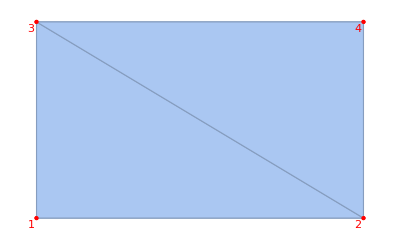

```mathematica
mr = MeshRegion[ncoor, Polygon /@ elnode,MeshCellStyle -> { 0 -> {PointSize[Large], Red}}]; 
  HighlightMesh[mr, {Labeled[0, "Index", {Top, Right},Style[#, Red] &], Labeled[2, "Index"]}]
```

#### Boundary Conditions

```mathematica
nforce ={{2,0,500},{4,0,500}};
```

```mathematica
ndispl = {{1,0,0},{3,0,0}};
```

## Calculation

Assembling Force Matrix

```mathematica
(* fsnode -> surface force at node *)
fsnode={nforce[[All,1]],thk nforce[[All,2]],thk nforce[[All,3]]};fsnode=Transpose@fsnode;
```

```mathematica
(* fs -> surface force matrix *)
fs=Array[0 &,{Length[ncoor],2}];
Do[
fs[[fsnode[[j,1]],i-1]]=fsnode[[j,i]]
,{i,2,3},{j,Length[fsnode]}
];
fs=ArrayReshape[fs,{2 Length[ncoor],1}];
```

```mathematica
fm=fs
```

{{0},{0},{0},{5000},{0},{0},{0},{5000}}

Assembling Displacement Matrix

```mathematica
(* dm -> displacement matrix *)
dm=Array[free &,{Length[ncoor],2}];
Do[
dm[[ndispl[[i,1]],j]]=ndispl[[i,j+1]]
,{i,Length[ndispl]},{j,2}];
dm=ArrayReshape[dm,{2 Length[ncoor],1}];
```

Assembling Global Stiffness Matrix

```mathematica
KG= Array[0 &,{2 Length[ncoor],2 Length[ncoor]}];
```

```mathematica
Do[
Part[KG,tr[el],tr[el]]+=km[el]
,{el,Length[elnode]}
];KG;
```

Reducing Stiffness Matrix

```mathematica
(* rl is the prescribed displacement node that is going to be eliminated *)
numberdof=Table[{i} ,{i,Length[dm]}];unrestained=Part[Position[dm,free],All,1];
rl=reducer[numberdof,unrestained,{}];rl=Flatten@rl;
```

```mathematica
rl
```

{1,2,5,6}

```mathematica
(* Reducting Global Stiffness Matrix *)
KR=reducer[KG,rl,rl];
```

```mathematica
(* Reducting Force Matrix *)
eliminator=Array[0 &, {Length[dm]}];Do[
eliminator+=Part[KG,All,rl[[j]]]*Part[dm,rl[[j]],1]
,{j,Length[rl]}
];
```

```mathematica
Fred=reducer[(fm-eliminator),rl,{}];
```

```mathematica
(* Solving reduction displacement matrix *)
Dred=Inverse[KR].Fred
```

{{1.60021×10^-9},{7.47623×10^-9},{-1.79378×10^-9},{8.05695×10^-9}}

```mathematica
(* DM -> complete dof displacement matrix*)
unknownDispl=Flatten[Position[Flatten@dm,free]];
Do[
dm[[unknownDispl[[i]]
]]=Dred[[i]]
,{i,Length[Dred]}];
```

```mathematica
(* fm -> Force / Reaction dof  *)
fm=KG.dm; fm//MatrixForm;
```

## Plotting Result

```mathematica
scalePlot=50; (* 0 -> undeformed, 1 -> actual deformed, >1 -> scaled deformed *)
```

```mathematica
(* DM -> displacement component matrix in x-y direction *)
DM=ArrayReshape[dm,{Length[ncoor],2}];
```

```mathematica
dcoor=ncoor+DM*scalePlot;
```

```mathematica
dcoor
```

{{0,0},{10.,3.73812×10^-7},{0,6},{10.,6.}}

```mathematica
(* nodal displacement in x-axis *)
DX=Part[DM,All,1]
```

{0,1.60021×10^-9,0,-1.79378×10^-9}

```mathematica
(* nodal displacement in y-axis *)
DY=Part[DM,All,2]
```

{0,7.47623×10^-9,0,8.05695×10^-9}

```mathematica
(* DU -> displacement magnitude/vector *)
DU=Array[0 &,{Length[ncoor]}];Do[
DU[[i]]=Sqrt[Part[DM,i,1]^2+Part[DM,i,2]^2],
{i,Length[ncoor]}
]
```

```mathematica
plottingResult[DU,"m","Deflection"]
```

-Graphics-